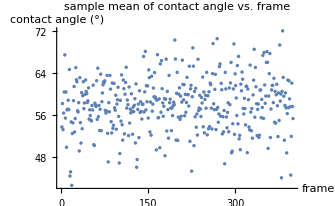

```mathematica
SetDirectory[NotebookDirectory[]];
rawdata=Flatten[Import["samplemeanvalue.dat","Data"]];
plt=ListPlot[rawdata,PlotRange->All,PlotLabel->"sample mean of contact angle vs. frame",AxesLabel->{"frame","contact angle (°)"}]
Length[rawdata];
Export["listplot.jpg",plt,ImageResolution->500];
```

```mathematica
Mean[rawdata]
```

58.088

```mathematica
SetDirectory[NotebookDirectory[]];
rawdata1=Flatten[Import["stddeviationvalue.dat","Data"]];
Length[rawdata1];
```

609887.

```mathematica
stddeviationofmeanofsamplemean=Sqrt[Sum[(rawdata1[[i]])^2,{i,1,Length[rawdata1]}]]/Length[rawdata1]
```

1.95238

```mathematica
data1={94.20264622658104,6.863311535332357,38.412255192535966,92.06956458796122,89.08787715832987,34.54261772068454,97.28897483027855,77.58615344865872,36.0036359568382,34.962862771302035,45.74439973619106,91.43372505631376,91.79657802470999,21.427998465094444,166.3206667725114,76.58730722146825,70.1266910063131,77.52199193001329,12.746034641326329,36.3844340718377,121.8061777989847,116.45480104608538,13.943934200387533,53.756804487533444,55.95446183479567,125.29708745168227,21.82110529921496,7.766441046384077,24.158166114870326,104.78920540501507,15.986812192273964,122.07614873620915,6.5278548675014125,63.19667822880073,12.793987317255825,16.24599250687043,42.59634413541214,10.043682477719177,26.322165961893013,94.24141489788109,36.0036359568382,8.221532721490036,63.19667822880073,101.86838897301156,74.66434414854787,103.46153508903319,37.45678654830992,68.51583055066638,4.360913067084466,99.4199726225128,16.841001285121667,24.355140765235053,26.293313203573753,41.43456550416289,20.484085077099127,14.711950941147423,28.068785266198425,122.47798875677788,22.748273704886227,94.41586557264863,16.71979588083524,32.61558205236901,94.20264622658104,70.1266910063131,16.403150233630175,36.0036359568382,77.52199193001329,85.92940742110643,57.61924113177709,93.74701564079967,19.032141550342995,37.519366903147485,121.52959733889055,70.09480023879605,7.901994589851478,115.16193281903053,142.25942560252977,12.795298263813422,41.09139060822525,35.376804983586126,103.46153508903319,58.71846860077989,57.61924113177709,53.82284821729008,34.62999329906521,15.700736320904221,19.70625363326811,104.22713859151845,43.916774165753544,19.458384483716515,55.953724235109824,25.36146403094674,34.6823794176403,12.48253272344648,19.080880388648012,24.903465554456258,17.822601576868852,63.19667822880073,15.700736320904221,115.7415666810185,67.40782601084594,29.88713573822352,138.94871816949424,54.73382815702141,41.50430627273762,20.200314946501695,67.40782601084594,11.927464089011623,18.304348408583866,45.88416483155969,7.907416950844253,23.588414582619546,38.06249255212771,5.3666208137700675,92.00218966138054,50.99158919498522,20.484085077099127,37.45678654830992,26.520365994060107,142.25942560252977,40.65446804846022,77.58615344865872,57.61924113177709,37.80801162178964,10.043682477719177,103.76292674056751,29.88713573822352,83.50640615691928,67.60570402640225,77.63894258094616,38.63439398802184,18.181843673697262,70.3300450539362,31.716637789271452,121.27604606900567,41.17524654116967,18.439336500796074,38.23699176325072,81.3252477349329,103.02462114726009,13.851067966505223,28.66398123870701,76.58730722146825,14.685177295415498,67.27949983550258,76.5938160325339,66.64325528220658,95.32209408840788,39.26835633128915,121.52959733889055,7.496052798168394,69.54682764661223,36.04994726497634,26.293313203573753,22.535489221023326,106.43161630190471,5.3666208137700675,67.27949983550258,147.8198870071455,78.39333596381618,45.5721192157431,44.504874296158185,103.6695779914784,94.39676446034763,34.145243190016,94.83366803824853,23.731909046868605,36.0036359568382,87.15964264025185,22.083512543302778,51.46674145473528,84.25680921493893,25.44951287275085,92.06956458796122,97.77451655189157,20.200314946501695,74.39216272159605,37.80606113642897,18.767909033531172,38.06033742039453,64.91148686044357,20.577815205989584,60.40814746750889,16.827407982404093,35.376804983586126,57.61924113177709,6.7351963067392875,7.723874233072449,55.555567087661835,29.770815124081444,122.92436278260213,46.241766069052936,18.181843673697262,130.79795573825763,115.7415666810185,142.25942560252977,17.822601576868852,42.52040511838187,20.422358584299985,5.804737411061883,121.27604606900567,26.293313203573753,45.1176806793415,89.63999688827884,14.794487738967304,23.731909046868605,49.13360148441534,17.270340939087355,102.03221439649447,16.71979588083524,18.709837943604118,76.5938160325339,50.04571666652086,12.199410416278152,37.80606113642897,113.76923831130054,74.71424943809998,26.351739015729013,95.32209408840788,116.45480104608538,12.550756544778185,35.90403121612764,121.16691144432664,19.080880388648012,97.64449176742247,68.177586685657,89.63999688827884,12.746034641326329,46.104134202669606,50.51592229941729,97.77451655189157,16.403150233630175,19.70625363326811,91.44342356126076,113.76923831130054,47.49475794740054,17.33769653094563,41.300685083136045,99.67292891271566,32.71577545718326,46.774338588695336,18.304348408583866,81.82924336497786,93.74701564079967,12.746034641326329,128.37792604738323,70.3300450539362,15.117458221418481,23.936891858781603,46.104134202669606,19.70625363326811,27.515339740492525,111.37904434426726,94.84502254770933,140.3778869949119,66.37373872257602,87.15964264025185,44.504874296158185,122.5847288336409,82.37248201415582,67.40782601084594,51.154027027571345,58.08363052099359,96.64440037471786,19.080880388648012,38.06033742039453,80.35984030796031,92.06956458796122,47.77036784473481,17.292117792875636,90.,57.61924113177709,85.47486149635421,13.943934200387533,80.91773587642504,71.90236062717383,91.44342356126076,46.104134202669606,7.907416950844253,10.166584491864478,18.304348408583866,18.16648222740059,16.42577545153486,132.46513003447777,21.27608991996727,64.91148686044357,93.74701564079967,122.5847288336409,122.5847288336409,134.42411838674343,33.74944382875414,91.79657802470999,121.16691144432664,93.79556740450032,102.02322649932884,89.08787715832987,58.908317982344286,34.27454875821461,11.927464089011623,114.92944256729083,46.774338588695336,81.3252477349329,42.59634413541214,14.16152229013168,116.45480104608538,40.32383693539915,21.84138562381725,16.403150233630175,76.79262438808489,20.577815205989584,66.35282134541752,28.400111161014948,46.82136131826696,71.90236062717383,12.55064458153022,41.300685083136045,16.827407982404093,58.08363052099359,4.360913067084466,12.199410416278152,53.334486192810445,16.46073052479928,55.95446183479567,30.67989405693546,92.9760322696735,97.01041121676253,92.9760322696735,67.60570402640225,41.300685083136045,27.57476437414901,10.45416972410269,66.64325528220658,8.649802540514793,34.145243190016,134.42411838674343,22.083512543302778,32.92239131151031,106.09354636393095,41.09139060822525,41.300685083136045,97.64449176742247,47.77036784473481,31.7549152433954,58.908317982344286,114.92944256729083,85.3885526485564,38.4955234275971,24.52735723327057,97.01212380012221,58.908317982344286,67.40782601084594,124.69038836342983,20.577815205989584,57.61924113177709,92.06956458796122,34.27454875821461,49.37820461366066,27.704283613441724,22.626049935844634,117.72409466018706,66.37373872257602,123.73097920158118,36.0036359568382,45.740175679875406,26.04468456222951,47.67944345831811,18.439336500796074,77.58615344865872,87.30438006943147,17.79503708370301,79.50936779205003,7.723874233072449,115.7415666810185,121.52959733889055,18.1245263883248,6.526808862729882,6.316443681305894,98.24616138007964,109.95334242810218,121.16691144432664,97.16987767978362,21.115093930408218,103.76292674056751,66.04860047115166,24.355140765235053,10.166584491864478,8.519457936135273,5.3666208137700675,19.095304213285004,21.01985706243514,17.292117792875636,93.75913322854151,19.032141550342995,19.080880388648012,99.67292891271566,7.740739169136178,10.043682477719177,22.083512543302778,14.246492963404767,84.34902192617713,42.078944830345286,93.75913322854151,44.504874296158185,66.64325528220658,27.515339740492525,31.7549152433954,33.73124733986734,13.992369891569295,24.355140765235053,32.287575027558304,25.36146403094674,18.304348408583866,85.7017682902567,13.887813836068027,37.80801162178964,45.991211226314235,94.83366803824853,12.21692790128419,167.36792433648225,17.822601576868852,27.74544300019268,28.714505268434284,91.42226887674389,60.40814746750889,55.1437099334061,13.851067966505223,30.310073251837586,63.19667822880073,128.21139462080524,63.911234654292436,67.40782601084594,94.83366803824853,50.2626955424017,85.43530743516486,90.47798863187877,32.25349223756499,50.04571666652086,32.25349223756499,22.083512543302778,6.7351963067392875,140.3778869949119,21.829866590769516,36.04994726497634,40.681198721828615,17.03167089196948,32.11301818572234,66.64325528220658,37.45678654830992,37.45678654830992,83.50640615691928,123.73097920158118,37.45678654830992,42.38699429079754,122.47798875677788,40.681198721828615,32.92239131151031,18.181843673697262,8.519457936135273,121.8061777989847,27.000109464265478,99.4199726225128,88.30056895011985,41.300685083136045,13.887813836068027,76.5938160325339,113.52485706169445,109.95334242810218,94.39676446034763,45.991211226314235,63.19667822880073,91.43372505631376,90.,29.553053090614263,5.3666208137700675,94.74692722522263,124.69038836342983,98.83355407566808,140.3778869949119,64.09964330764386,36.0036359568382,38.06249255212771,21.427998465094444,55.76688831526698,7.109351015166783,28.714505268434284,26.293313203573753,14.740251719769647,18.767909033531172,14.431757401184464,25.36146403094674,18.41816820887866,15.06998121337498,93.75913322854151,16.827407982404093,5.804737411061883,113.26309711467232,27.101843396034774,7.169669542021075,41.300685083136045,60.748277013734445,85.3885526485564,53.68510732837239,10.314841257529828,90.36734050841407,18.181843673697262,20.101303934791428,113.77679726618341,7.169669542021075,77.65268461823992,26.04468456222951,102.02322649932884,25.700850639151888,103.6695779914784,77.63894258094616,17.292117792875636,142.25942560252977,17.79503708370301,75.6293998829248,98.83355407566808,34.343318086961126,38.06033742039453,49.37820461366066,54.484514675838206,71.91673835369467,16.71979588083524,75.6293998829248,50.2626955424017,116.25945706257735,111.9547056963761,5.3666208137700675,98.00561768137283,18.559819333829093,6.316443681305894,70.98304578318275,93.79556740450032,30.67989405693546,74.66434414854787,119.13384833602012,36.0036359568382,15.117458221418481,12.21692790128419,17.822601576868852,15.75918340275754,18.38093976956982,90.,85.92940742110643,90.,134.42411838674343,128.21139462080524,32.92239131151031,81.82924336497786,64.96608187222373,92.9760322696735,15.06998121337498,50.7168132218336,17.615681571240017,22.741037026702475,90.,32.25349223756499,8.519457936135273,66.64325528220658,7.169669542021075,70.98304578318275,67.40782601084594,17.28968045155749,114.92944256729083,102.64185224659437,139.21812620891615,16.71979588083524,7.293680756916826,32.07523805416877,21.009923909070093,21.115093930408218,91.79657802470999,16.206156939864265,92.06956458796122,85.43530743516486,21.940324577578604,7.169669542021075,167.36792433648225,29.88713573822352,38.309875660236145,15.700736320904221,55.95446183479567,36.3844340718377,21.940324577578604,124.69038836342983,103.6695779914784,89.08787715832987,74.73667670216729,20.577815205989584,57.89057807585336,1.344052683471414,18.709837943604118,78.09335741083544,121.8061777989847,130.06089202984913,128.21139462080524,11.11538101403988,81.82924336497786,70.98304578318275,63.19667822880073,49.37820461366066,29.553053090614263,35.90403121612764,85.43530743516486,78.09335741083544,37.80801162178964,25.36146403094674,117.72409466018706,36.50344038714385,34.962862771302035,24.532748353006465,114.92944256729083,36.3844340718377,5.3666208137700675,64.91148686044357,92.06956458796122,148.76653531183678,94.37677019437508,37.519366903147485,14.367957726126836,91.43372505631376,19.70625363326811,30.67578793536463,98.00561768137283,66.76390921496123,68.177586685657,45.991211226314235,47.49027112214147,45.1176806793415,13.851067966505223,139.21812620891615,18.16648222740059,23.885936514817907,6.209033579711524,25.720254336760966,127.62106853931742,113.77679726618341,41.300685083136045,90.13949476579768,12.55064458153022,16.827407982404093,117.22772872518823,101.86838897301156,82.0017726652259,10.45416972410269,91.43372505631376,94.83366803824853,97.77451655189157,64.91148686044357,47.49475794740054,85.92940742110643,50.99158919498522,16.71979588083524,127.62106853931742,22.741037026702475,32.07523805416877,13.887813836068027,78.09335741083544,32.25349223756499,34.22569753302655,87.4901314765271,20.200314946501695,14.740251719769647,98.83355407566808,32.71577545718326,23.588414582619546,97.01212380012221,51.154027027571345,41.17524654116967,29.88713573822352,25.700850639151888,136.91284172187636,42.078944830345286,32.07523805416877,10.45416972410269,36.3844340718377,70.3300450539362,14.685177295415498,67.27949983550258,90.,45.1176806793415,101.74467117736533,17.753937229381965,18.042325941648425,6.526808862729882,87.46287883190632,110.70645951522759,104.78920540501507,142.25942560252977,154.78474236644834,32.07523805416877,73.94825983360995,38.23699176325072,92.9760322696735,8.660282787744634,66.64325528220658,54.903172653354616,59.98598234594718,132.46513003447777,44.62385081182915,102.15320931383275,21.84138562381725,112.43263798638691,26.393906985737264,115.7415666810185,121.56441346145328,71.90236062717383,101.61127662337658,10.166584491864478,12.21692790128419,15.986812192273964,24.158166114870326,64.91148686044357,71.61429884767406,63.911234654292436,22.626049935844634,94.37677019437508,34.62999329906521,94.24141489788109,10.043682477719177,93.74701564079967,66.64325528220658,76.5938160325339,14.248758831931575,7.901994589851478,135.18849707096658,30.67989405693546,32.92239131151031,35.35696878617461,134.42411838674343,18.38093976956982,55.555567087661835,32.11301818572234,35.515814773849044,89.08787715832987,34.54261772068454,99.29434126157301,96.64440037471786,37.519366903147485,8.221532721490036,122.5847288336409,14.367957726126836,51.62101845435715,99.02035429794816,33.99259102016696,30.310073251837586,115.16193281903053,90.,66.04860047115166,19.33078144169828,10.043682477719177,75.6293998829248,28.994408034513896,101.86838897301156,93.18143632272067,117.22772872518823,99.67292891271566,83.50640615691928,8.519457936135273,5.3666208137700675,139.21812620891615,21.940324577578604,76.79262438808489,32.25349223756499,13.502806087034507,92.57097620033883,94.20264622658104,140.3778869949119,95.42073124003782,23.588414582619546,22.535489221023326,46.98776188845527,90.,51.154027027571345,112.75392987753052,51.154027027571345,22.231465483163678,51.154027027571345,17.292117792875636,147.8198870071455,66.35282134541752,139.21812620891615,118.62708806792315,93.75913322854151,16.46073052479928,90.,12.793987317255825,19.046872707100103,154.78474236644834,9.980311258404292,24.355140765235053,76.5938160325339,37.519366903147485,69.54682764661223,74.66434414854787,101.86838897301156,10.854805366299061,18.439336500796074,41.300685083136045,45.10390544501277,11.927464089011623,18.16648222740059,18.1245263883248,74.80474414202048,92.57097620033883,33.21566863114911,34.145243190016,82.0017726652259,16.71979588083524,27.704283613441724,74.71424943809998,5.934632778102134,21.036734810772426,93.75913322854151,7.766441046384077,29.88713573822352,104.97609837186968,82.77612333174324,10.166584491864478,121.56441346145328,15.986812192273964,44.62385081182915,23.731909046868605,140.3778869949119,18.767909033531172,77.58615344865872,99.4199726225128,37.80606113642897,91.43372505631376,91.79657802470999,58.91093426578901,24.355140765235053,16.71979588083524,36.0036359568382,89.08787715832987,23.108460231624978,18.439336500796074,52.15794354959801,45.991211226314235,100.36338602417771,14.16152229013168,108.50138569372285,13.785707787678243,14.16152229013168,14.246492963404767,77.23711319166006,34.145243190016,7.85967021130592,78.29570433111098,94.83366803824853,15.986812192273964,15.117458221418481,70.64730123478812,46.774338588695336,12.550756544778185,15.912017847213693,134.42411838674343,15.538549285090813,94.39676446034763,15.117458221418481,4.480901303634748,40.65446804846022,18.559819333829093,24.355140765235053,17.75704049442119,36.25753049735739,23.885936514817907,58.91093426578901,93.69216605603137,4.415252533444196,78.09335741083544,30.773719871311975,103.76292674056751,19.70625363326811,76.58730722146825,34.962862771302035,15.986812192273964,16.71979588083524,102.64185224659437,127.62106853931742,12.48253272344648,21.009923909070093,142.25942560252977,32.07523805416877,55.95446183479567,25.700850639151888,36.25753049735739,41.300685083136045,11.927464089011623,16.827407982404093,88.04293375624879,34.145243190016,19.080880388648012,37.80801162178964,36.04994726497634,18.38093976956982,134.42411838674343,35.515814773849044,47.49475794740054,24.355140765235053,90.47798863187877,104.22713859151845,74.66434414854787,29.88713573822352,70.3300450539362,23.731909046868605,66.35282134541752,57.61924113177709,45.740175679875406,15.117458221418481,28.145024428912375,25.44951287275085,45.54414105742856,30.67989405693546,93.90237080934725,20.577815205989584,45.1176806793415,15.75918340275754,63.19667822880073,21.036734810772426,98.00561768137283,45.1176806793415,17.822601576868852,77.63894258094616,16.403150233630175,11.927464089011623,20.101303934791428,123.73097920158118,20.484085077099127,111.37904434426726,26.06602592246588,15.117458221418481,20.76332692004696,44.62385081182915,24.355140765235053,57.61924113177709,67.27949983550258,38.06033742039453,57.89057807585336,114.92944256729083,6.209033579711524,13.785707787678243,21.82110529921496,37.80801162178964,36.93597782937927,44.17761321619716,115.16193281903053,67.27949983550258,15.06998121337498,104.97609837186968,116.45480104608538,22.626049935844634,15.06998121337498,32.07523805416877,8.727671892245695,16.42577545153486,40.32383693539915,6.232668556462213,121.8061777989847,136.91284172187636,77.3221814457934,53.334486192810445,41.17524654116967,30.773719871311975,93.79556740450032,6.5278548675014125,136.04935075267394,32.07523805416877,46.774338588695336,45.740175679875406,11.927464089011623,7.293680756916826,34.62999329906521,18.16648222740059,148.76653531183678,17.686130634089697,64.09964330764386,55.953724235109824,45.88416483155969,113.76923831130054,36.04994726497634,44.504874296158185,100.07179514229304,28.23973562128413,93.74701564079967,94.37677019437508,36.0036359568382,71.91673835369467,35.376804983586126,85.80177505975448,46.98776188845527,19.654598566710064,13.851067966505223,7.901994589851478,27.088976480096502,97.77451655189157,41.43456550416289,66.64325528220658}
```

{94.2026,6.86331,38.4123,92.0696,89.0879,34.5426,97.289,77.5862,36.0036,34.9629,45.7444,91.4337,91.7966,21.428,166.321,76.5873,70.1267,77.522,12.746,36.3844,121.806,116.455,13.9439,53.7568,55.9545,125.297,21.8211,7.76644,24.1582,104.789,15.9868,122.076,6.52785,63.1967,12.794,16.246,42.5963,10.0437,26.3222,94.2414,36.0036,8.22153,63.1967,101.868,74.6643,103.462,37.4568,68.5158,4.36091,99.42,16.841,24.3551,26.2933,41.4346,20.4841,14.712,28.0688,122.478,22.7483,94.4159,16.7198,32.6156,94.2026,70.1267,16.4032,36.0036,77.522,85.9294,57.6192,93.747,19.0321,37.5194,121.53,70.0948,7.90199,115.162,142.259,12.7953,41.0914,35.3768,103.462,58.7185,57.6192,53.8228,34.63,15.7007,19.7063,104.227,43.9168,19.4584,55.9537,25.3615,34.6824,12.4825,19.0809,24.9035,17.8226,63.1967,15.7007,115.742,67.4078,29.8871,138.949,54.7338,41.5043,20.2003,67.4078,11.9275,18.3043,45.8842,7.90742,23.5884,38.0625,5.36662,92.0022,50.9916,20.4841,37.4568,26.5204,142.259,40.6545,77.5862,57.6192,37.808,10.0437,103.763,29.8871,83.5064,67.6057,77.6389,38.6344,18.1818,70.33,31.7166,121.276,41.1752,18.4393,38.237,81.3252,103.025,13.8511,28.664,76.5873,14.6852,67.2795,76.5938,66.6433,95.3221,39.2684,121.53,7.49605,69.5468,36.0499,26.2933,22.5355,106.432,5.36662,67.2795,147.82,78.3933,45.5721,44.5049,103.67,94.3968,34.1452,94.8337,23.7319,36.0036,87.1596,22.0835,51.4667,84.2568,25.4495,92.0696,97.7745,20.2003,74.3922,37.8061,18.7679,38.0603,64.9115,20.5778,60.4081,16.8274,35.3768,57.6192,6.7352,7.72387,55.5556,29.7708,122.924,46.2418,18.1818,130.798,115.742,142.259,17.8226,42.5204,20.4224,5.80474,121.276,26.2933,45.1177,89.64,14.7945,23.7319,49.1336,17.2703,102.032,16.7198,18.7098,76.5938,50.0457,12.1994,37.8061,113.769,74.7142,26.3517,95.3221,116.455,12.5508,35.904,121.167,19.0809,97.6445,68.1776,89.64,12.746,46.1041,50.5159,97.7745,16.4032,19.7063,91.4434,113.769,47.4948,17.3377,41.3007,99.6729,32.7158,46.7743,18.3043,81.8292,93.747,12.746,128.378,70.33,15.1175,23.9369,46.1041,19.7063,27.5153,111.379,94.845,140.378,66.3737,87.1596,44.5049,122.585,82.3725,67.4078,51.154,58.0836,96.6444,19.0809,38.0603,80.3598,92.0696,47.7704,17.2921,90.,57.6192,85.4749,13.9439,80.9177,71.9024,91.4434,46.1041,7.90742,10.1666,18.3043,18.1665,16.4258,132.465,21.2761,64.9115,93.747,122.585,122.585,134.424,33.7494,91.7966,121.167,93.7956,102.023,89.0879,58.9083,34.2745,11.9275,114.929,46.7743,81.3252,42.5963,14.1615,116.455,40.3238,21.8414,16.4032,76.7926,20.5778,66.3528,28.4001,46.8214,71.9024,12.5506,41.3007,16.8274,58.0836,4.36091,12.1994,53.3345,16.4607,55.9545,30.6799,92.976,97.0104,92.976,67.6057,41.3007,27.5748,10.4542,66.6433,8.6498,34.1452,134.424,22.0835,32.9224,106.094,41.0914,41.3007,97.6445,47.7704,31.7549,58.9083,114.929,85.3886,38.4955,24.5274,97.0121,58.9083,67.4078,124.69,20.5778,57.6192,92.0696,34.2745,49.3782,27.7043,22.626,117.724,66.3737,123.731,36.0036,45.7402,26.0447,47.6794,18.4393,77.5862,87.3044,17.795,79.5094,7.72387,115.742,121.53,18.1245,6.52681,6.31644,98.2462,109.953,121.167,97.1699,21.1151,103.763,66.0486,24.3551,10.1666,8.51946,5.36662,19.0953,21.0199,17.2921,93.7591,19.0321,19.0809,99.6729,7.74074,10.0437,22.0835,14.2465,84.349,42.0789,93.7591,44.5049,66.6433,27.5153,31.7549,33.7312,13.9924,24.3551,32.2876,25.3615,18.3043,85.7018,13.8878,37.808,45.9912,94.8337,12.2169,167.368,17.8226,27.7454,28.7145,91.4223,60.4081,55.1437,13.8511,30.3101,63.1967,128.211,63.9112,67.4078,94.8337,50.2627,85.4353,90.478,32.2535,50.0457,32.2535,22.0835,6.7352,140.378,21.8299,36.0499,40.6812,17.0317,32.113,66.6433,37.4568,37.4568,83.5064,123.731,37.4568,42.387,122.478,40.6812,32.9224,18.1818,8.51946,121.806,27.0001,99.42,88.3006,41.3007,13.8878,76.5938,113.525,109.953,94.3968,45.9912,63.1967,91.4337,90.,29.5531,5.36662,94.7469,124.69,98.8336,140.378,64.0996,36.0036,38.0625,21.428,55.7669,7.10935,28.7145,26.2933,14.7403,18.7679,14.4318,25.3615,18.4182,15.07,93.7591,16.8274,5.80474,113.263,27.1018,7.16967,41.3007,60.7483,85.3886,53.6851,10.3148,90.3673,18.1818,20.1013,113.777,7.16967,77.6527,26.0447,102.023,25.7009,103.67,77.6389,17.2921,142.259,17.795,75.6294,98.8336,34.3433,38.0603,49.3782,54.4845,71.9167,16.7198,75.6294,50.2627,116.259,111.955,5.36662,98.0056,18.5598,6.31644,70.983,93.7956,30.6799,74.6643,119.134,36.0036,15.1175,12.2169,17.8226,15.7592,18.3809,90.,85.9294,90.,134.424,128.211,32.9224,81.8292,64.9661,92.976,15.07,50.7168,17.6157,22.741,90.,32.2535,8.51946,66.6433,7.16967,70.983,67.4078,17.2897,114.929,102.642,139.218,16.7198,7.29368,32.0752,21.0099,21.1151,91.7966,16.2062,92.0696,85.4353,21.9403,7.16967,167.368,29.8871,38.3099,15.7007,55.9545,36.3844,21.9403,124.69,103.67,89.0879,74.7367,20.5778,57.8906,1.34405,18.7098,78.0934,121.806,130.061,128.211,11.1154,81.8292,70.983,63.1967,49.3782,29.5531,35.904,85.4353,78.0934,37.808,25.3615,117.724,36.5034,34.9629,24.5327,114.929,36.3844,5.36662,64.9115,92.0696,148.767,94.3768,37.5194,14.368,91.4337,19.7063,30.6758,98.0056,66.7639,68.1776,45.9912,47.4903,45.1177,13.8511,139.218,18.1665,23.8859,6.20903,25.7203,127.621,113.777,41.3007,90.1395,12.5506,16.8274,117.228,101.868,82.0018,10.4542,91.4337,94.8337,97.7745,64.9115,47.4948,85.9294,50.9916,16.7198,127.621,22.741,32.0752,13.8878,78.0934,32.2535,34.2257,87.4901,20.2003,14.7403,98.8336,32.7158,23.5884,97.0121,51.154,41.1752,29.8871,25.7009,136.913,42.0789,32.0752,10.4542,36.3844,70.33,14.6852,67.2795,90.,45.1177,101.745,17.7539,18.0423,6.52681,87.4629,110.706,104.789,142.259,154.785,32.0752,73.9483,38.237,92.976,8.66028,66.6433,54.9032,59.986,132.465,44.6239,102.153,21.8414,112.433,26.3939,115.742,121.564,71.9024,101.611,10.1666,12.2169,15.9868,24.1582,64.9115,71.6143,63.9112,22.626,94.3768,34.63,94.2414,10.0437,93.747,66.6433,76.5938,14.2488,7.90199,135.188,30.6799,32.9224,35.357,134.424,18.3809,55.5556,32.113,35.5158,89.0879,34.5426,99.2943,96.6444,37.5194,8.22153,122.585,14.368,51.621,99.0204,33.9926,30.3101,115.162,90.,66.0486,19.3308,10.0437,75.6294,28.9944,101.868,93.1814,117.228,99.6729,83.5064,8.51946,5.36662,139.218,21.9403,76.7926,32.2535,13.5028,92.571,94.2026,140.378,95.4207,23.5884,22.5355,46.9878,90.,51.154,112.754,51.154,22.2315,51.154,17.2921,147.82,66.3528,139.218,118.627,93.7591,16.4607,90.,12.794,19.0469,154.785,9.98031,24.3551,76.5938,37.5194,69.5468,74.6643,101.868,10.8548,18.4393,41.3007,45.1039,11.9275,18.1665,18.1245,74.8047,92.571,33.2157,34.1452,82.0018,16.7198,27.7043,74.7142,5.93463,21.0367,93.7591,7.76644,29.8871,104.976,82.7761,10.1666,121.564,15.9868,44.6239,23.7319,140.378,18.7679,77.5862,99.42,37.8061,91.4337,91.7966,58.9109,24.3551,16.7198,36.0036,89.0879,23.1085,18.4393,52.1579,45.9912,100.363,14.1615,108.501,13.7857,14.1615,14.2465,77.2371,34.1452,7.85967,78.2957,94.8337,15.9868,15.1175,70.6473,46.7743,12.5508,15.912,134.424,15.5385,94.3968,15.1175,4.4809,40.6545,18.5598,24.3551,17.757,36.2575,23.8859,58.9109,93.6922,4.41525,78.0934,30.7737,103.763,19.7063,76.5873,34.9629,15.9868,16.7198,102.642,127.621,12.4825,21.0099,142.259,32.0752,55.9545,25.7009,36.2575,41.3007,11.9275,16.8274,88.0429,34.1452,19.0809,37.808,36.0499,18.3809,134.424,35.5158,47.4948,24.3551,90.478,104.227,74.6643,29.8871,70.33,23.7319,66.3528,57.6192,45.7402,15.1175,28.145,25.4495,45.5441,30.6799,93.9024,20.5778,45.1177,15.7592,63.1967,21.0367,98.0056,45.1177,17.8226,77.6389,16.4032,11.9275,20.1013,123.731,20.4841,111.379,26.066,15.1175,20.7633,44.6239,24.3551,57.6192,67.2795,38.0603,57.8906,114.929,6.20903,13.7857,21.8211,37.808,36.936,44.1776,115.162,67.2795,15.07,104.976,116.455,22.626,15.07,32.0752,8.72767,16.4258,40.3238,6.23267,121.806,136.913,77.3222,53.3345,41.1752,30.7737,93.7956,6.52785,136.049,32.0752,46.7743,45.7402,11.9275,7.29368,34.63,18.1665,148.767,17.6861,64.0996,55.9537,45.8842,113.769,36.0499,44.5049,100.072,28.2397,93.747,94.3768,36.0036,71.9167,35.3768,85.8018,46.9878,19.6546,13.8511,7.90199,27.089,97.7745,41.4346,66.6433}

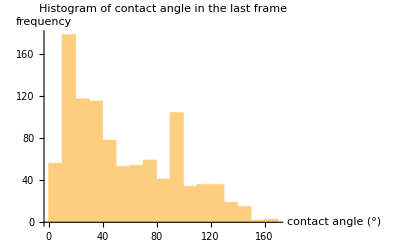

```mathematica
Histogram[data1,PlotLabel-> "Histogram of contact angle in the last frame",AxesLabel->{"contact angle (°)","frequency"}]
```